Under the assumption of an isotropic tissue

```mathematica
E1 = (n-1)(K/2(A-Ab)^2+G/2 P^2+L P)+Lw Pw;
```

Completing the square, done manually because this version of Mathematica doesn’t have the function yet

```mathematica
E2 = (n-1)(K/2(A-Ab)^2+G/2(P+L/(2G))^2-L^2/(4G))+Lw Pw;
```

Assuming a regular polygon network, where r is a function of the number of sides of the polygon

```mathematica
s1 = E2/.P-> (A/r)^(1/2) /.Pw-> (Aw/r)^(1/2)/. A -> (Ab n-Aw)/(n-1);
```

Dimensionless form

```mathematica
s2 = s1/(K Ab^2);
```

Change of variables

```mathematica
s3 = s2/. Aw -> Ab aw /. G -> g K Ab /. L -> l K Ab^(3/2) /. Lw -> lw K Ab^(3/2); 
s4 = s3/. K -> 1/. Ab -> 1/.aw -> pw^2 r/.l-> - 2 g b;
f = Collect[FactorTerms[Simplify[s4,pw>0],pw],pw,Simplify];
```

Derivative

```mathematica
df = D[(f), pw];
```

Taylor Expansion

```mathematica
lindf = Collect[FactorTerms[Normal[Series[df/.n -> 1/x,{x,0,1}]]/.x-> 1/n ,pw] ,pw,Expand];
```

Free field solution

```mathematica
lindffree = lindf/.lw-> 0;
lsimplified = lindffree/.r-> 1/(4 Pi);
S = Solve[lindffree==0,pw];
R = Solve[{lindf/.lw-> 4 b g}==0,pw];

lindffree
```

pw (-g+(b g)/(√(1/r))-(b g)/(2 n √(1/r))-(2 r)/n)+pw^3 ((b g)/(2 n (1/r)^(3/2))+(2 r^2)/n)

We will derive some typical thermodynamic properties of the tissue (like the “specific heat” of the tissue and the susceptibility to the actin-myosin band tension)

Specific heat for linearized energy (near critical point) (*sC = -b*∂_b (∂_b (f));  Specific heat*)

```mathematica
flin = Collect[FactorTerms[ ∫(lindf)ⅆpw,pw] ,pw,Expand]
lsC = -b*D[(D[(flin), b]), b]
```

lw pw+pw^2 (-g/2+(b g)/(2 √(1/r))-(b g)/(4 n √(1/r))-r/n)+pw^4 ((b g)/(8 n (1/r)^(3/2))+r^2/(2 n))

0

These results suggests that the specific heat at least for the linearized version of energy is (β-bx)^-α, with critical exponent α = 0

Coefficients from the polynomial

```mathematica
coefa = (-g+(b g)/(√(1/r))-(b g)/(2 n √(1/r))-(2 r)/n);

coefb = ((b g)/(2 n (1/r)^(3/2))+(2 r^2)/n);
pcrit = (lw/coefb)^(1/3);
```

(* 
xiCrit1 = Simplify[Abs[∂_lw pcrit]]; Susceptibility near critical point *)
(* Assuming Susceptibility satisfies ∂_lw p = 1/(2 a + 6 b  p^2) *)
(* Zero field susceptibility *)

```mathematica
xi2 = 1/(coefa + 3 coefb  pw^2);
xiCrit22 =Abs[ xi2/.pw-> pcrit]
```

1/Abs[-g+(b g)/(√(1/r))-(b g)/(2 n √(1/r))-(2 r)/n+3 (lw/((b g)/(2 n (1/r)^(3/2))+(2 r^2)/n))^(2/3) ((b g)/(2 n (1/r)^(3/2))+(2 r^2)/n)]

Looking at susceptibility for different number of cells shows that the qualitative behavior doesn’t change, still diverging at the critical point

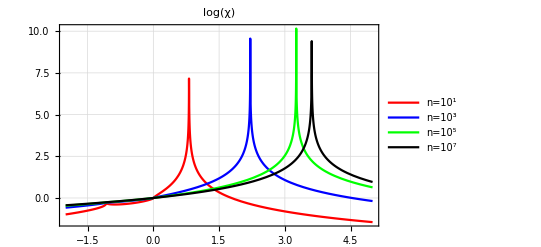

```mathematica
ps1 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Red,PlotRange->All,PlotLegends-> {"n=10^1"},Frame->True,GridLines->Automatic];
ps2 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 1000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Blue,PlotRange->All,PlotLegends-> {"n=10^3"},Frame->True,GridLines->Automatic];
ps3 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 100000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Green,PlotRange->All,PlotLegends-> {"n=10^5"},Frame->True,GridLines->Automatic];
ps4 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Black,PlotRange->All,PlotLegends-> {"n=10^7"},Frame->True,GridLines->Automatic];
Show[ps1,ps2,ps3, ps4,PlotLabel->Log[χ],AxesLabel->{β},LabelStyle->Directive[Bold]]
```

Looking at susceptibility for different regular polygon networks shows that the qualitative behavior doesn’t  change as well, still diverging at the critical point

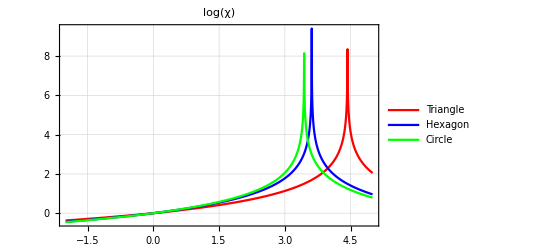

```mathematica
ps1 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(12 √3)},{b,-2,5},PlotStyle->Red,PlotRange->All,PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
ps2 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Blue,PlotRange->All,PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
ps3 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(4Pi)},{b,-2,5},PlotStyle->Green,PlotRange->All,PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];
Show[ps1,ps2,ps3,PlotLabel->Log[χ],AxesLabel->{β},LabelStyle->Directive[Bold]]
```

This behavior suggests that the susceptibility near the critical point behaves as (β-bx)^-γ, which suggests the critical exponent associated with it is γ = 1;

```mathematica
r1 = R[[1]][[1]];
r2 = R[[2]][[1]];
r3 = R[[3]][[1]];
(*Roots for free field case*)
rr1 = pw/.r1;
rr2 = pw/.r2;
rr3 =pw/.r3;
```

```mathematica
l1 = Limit[rr1,n->Infinity];
l2 = Limit[rr2,n->0];
l3 = Limit[rr3,n->0];
```

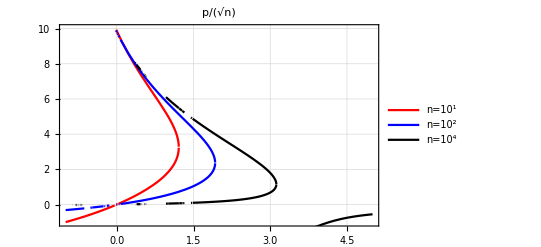

```mathematica
p1 = Plot[{rr1/.n-> 10/.r-> 1/(8 √3)/.g-> 1,
rr2/.n-> 10/.r->1/(8 √3)/.g-> 1,
rr3/.n-> 10/.r->1/(8 √3)/.g-> 1}/Sqrt[10],{b,-1,5},PlotStyle->Red,PlotRange->{-1,10},PlotLegends-> {"n=10^1"},Frame->True,GridLines->Automatic];
p2 = Plot[{rr1/.n-> 10^2/.r-> 1/(8 √3)/.g-> 1,
rr2/.n-> 10^2/.r->1/(8 √3)/.g-> 1,
rr3/.n-> 10^2/.r->1/(8 √3)/.g->1}/Sqrt[10^2],{b,-1,5},PlotStyle->Blue,PlotLegends-> {"n=10^2"}];
p3 = Plot[{rr1/.n-> 10^4/.r->1/(8 √3)/.g-> 1,
rr2/.n-> 10^4/.r-> 1/(8 √3)/.g-> 1,
rr3/.n-> 10^4/.r-> 1/(8 √3)/.g-> 1}/Sqrt[10^4],{b,-1,5},PlotStyle->Black,PlotLegends-> {"n=10^4"}];
Show[p1,p2,p3,PlotLabel->Style[p/Sqrt[n],18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

This behavior suggests that the susceptibility near the critical point behaves as (b-bx)^(-1/2), which suggests the critical exponent associated with it is 1/2;

These values for the critical exponents are expected, as the expression for energy we have is effectively a mean field approximation of the vertex model. This suggests the dynamic change in wound area evolution is intrinsically connected with the state properties of the tissue, and for a free-field case (in the absence of actin-myosin tension) the closure process can occur if the tissue is in a fluid-like state, with the critical point for the parameter b corresponding to the critical parameter p0 in the classical vertex model phase diagram by Staple et al (for the thermodynamic limit as n approaches infinity).

```mathematica
(*Toy model*)
Simplify[coefa/.r-> 1/bx^2/.g-> 1,bx>0]
Simplify[coefb/.r-> 1/bx^2/.g-> 1,bx>0]
rb1 = Simplify[rr1,{g>0,r>0,n>0}]
rb2 = Simplify[rr2,{g>0,r>0,n>0}]
rb3 = Simplify[rr3,{g>0,r>0,n>0}]
Manipulate[Plot[{Sqrt[(-(x-b)/b)/((x-b)/b+1)],-Sqrt[(-(x-b)/b)/((x-b)/b+1)]},{x,-0.1,3}],{b,0.1,2}]
```

-(4+b bx-2 b bx n+2 bx^2 n)/(2 bx^2 n)

(4+b bx)/(2 bx^4 n)

(2 3^(1/3) b g^2 n+3^(1/3) b^2 g^2 √r+8 3^(1/3) g n √r-2 3^(1/3) b^2 g^2 n √r+8 3^(1/3) b g r-8 3^(1/3) b g n r+16 3^(1/3) r^(3/2)+√r (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(2/3))/(3^(2/3) (b g r+4 r^(3/2)) (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(1/3))

(ⅈ (-(3^(1/3) (-ⅈ+√3) (g n (2-2 b √r)+b g √r+4 r))/r+((ⅈ+√3) (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(2/3))/(b g √r+4 r)))/(2 3^(2/3) (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(1/3))

-(ⅈ (-(3^(1/3) (ⅈ+√3) (g n (2-2 b √r)+b g √r+4 r))/r+((-ⅈ+√3) (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(2/3))/(b g √r+4 r)))/(2 3^(2/3) (-36 b^3 g^3 n-288 b^2 g^2 n √r-576 b g n r+√3 √(432 b^2 g^2 n^2 (b g+4 √r)^4-(4+(b g)/(√r))^3 r^(3/2) (b (g-2 g n)+(2 (g n+2 r))/(√r))^3))^(1/3))

```mathematica
Bc = b/.Solve[(√(g n (2-2 b √r)+b g √r+4 r))/(√(b g r^(3/2)+4 r^2))==0,b][[1]]
```

(2 (g n+2 r))/(g (-1+2 n) √r)

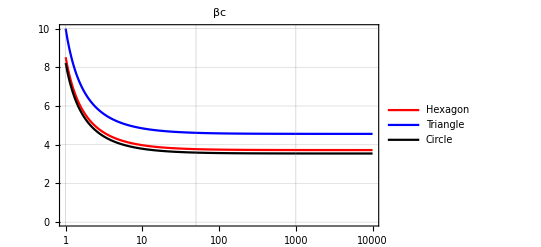

```mathematica
p1 = LogLinearPlot[{Bc/.r-> 1/(8 √3)/.g-> 1},{n,10^0,10^4},PlotStyle->Red,PlotRange->{0,10},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p2 = LogLinearPlot[{Bc/.r-> 1/(12 √3)/.g-> 1},{n,10^0,10^4},PlotStyle->Blue,PlotRange->{0,10},PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
p3 = LogLinearPlot[{Bc/.r-> 1/(4Pi)/.g-> 1},{n,10^0,10^4},PlotStyle->Black,PlotRange->{0,10},PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];
Show[p1,p2,p3,PlotLabel->Style[βc,18],AxesLabel->{Style[n,18]},LabelStyle->Directive[Bold]]
```

```mathematica
List1 = {0.655,0.677,0.699,0.703,0.708,0.712,0.714,0.7151,0.7153,0.716,0.721,0.725,0.730,0.734,0.738,0.743};
List2 = {3.04,2.72,2.11,1.91,1.66,1.34,1.15,1.093,1.090,0.395,0.182,0.177,0.171,0.166,0.170,0.162};
data  = Transpose@{List1*Sqrt[5.24],List2};
```

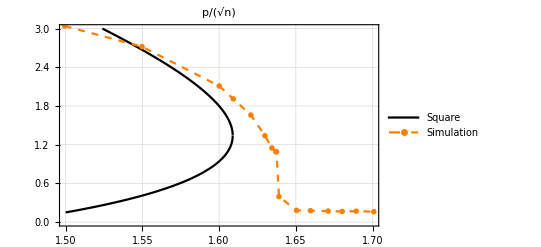

```mathematica
p1 = Plot[{rr1/.n-> 25/.r-> 1/(12 √3)/.g-> 1,
rr2/.n-> 25/.r->1/(12 √3)/.g-> 1,
rr3/.n-> 25/.r->1/(12 √3)/.g-> 1}/Sqrt[25],{b,1,2},PlotStyle->Red,PlotRange->{0,8},PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
p2 = Plot[{rr1/.n-> 25/.r-> 1/16/.g-> 1,
rr2/.n-> 25/.r->1/16/.g-> 1,
rr3/.n-> 25/.r->1/16/.g-> 1}/(Sqrt[25]),{b,1.5,1.7},PlotStyle->Black,PlotRange->{0,5},PlotLegends-> {"Square"},Frame->True,GridLines->Automatic];
p3 = Plot[{rr1/.n-> 25/.r-> 1/(8 √3)/.g-> 1,
rr2/.n-> 25/.r->1/(8 √3)/.g-> 1,
rr3/.n-> 25/.r->1/(8 √3)/.g-> 1}/Sqrt[25],{b,1,2},PlotStyle->Blue,PlotRange->{-1,10},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p4 = Plot[{rr1/.n-> 25/.r-> 1/(4Pi)/.g-> 1,
rr2/.n-> 25/.r->1/(4Pi)/.g-> 1,
rr3/.n-> 25/.r->1/(4Pi)/.g-> 1}/Sqrt[25],{b,1,2},PlotStyle->Green,PlotRange->{-1,10},PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];
p5 = ListPlot[data,Joined->True, PlotMarkers-> {-Graphics-, Medium},PlotStyle->{{Orange,Dashed}},PlotLegends-> {"Simulation"}];
p6 = Plot[{rr1/.n-> 25/.r-> 1/16/.g-> 1,
rr2/.n-> 25/.r->1/16/.g-> 1,
rr3/.n-> 25/.r->1/16/.g-> 1}^2/(16*Sqrt[25]*4/3)-1,{b,1.5,1.7},PlotStyle->Black,PlotRange->{0,3},PlotLegends-> {"Square"},Frame->True,GridLines->Automatic];


Show[p6,p5,PlotLabel->Style[p/Sqrt[n],18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

```mathematica
1/(4 n Tan[Pi/n])/.n->3
```

1/(12 √3)

```mathematica
N[1/(12 √3)]
```

0.0481125

```mathematica
N[1/16]
```

0.0625

```mathematica
N[1/20 √(1+2/(√5))]
```

0.0688191

```mathematica
data
```

{{1.49936,4.73011},{1.54972,4.2322},{1.60008,3.28307},{1.60924,2.97188},{1.62069,2.58289},{1.62984,2.08498},{1.63442,1.78935},{1.63694,1.70066},{1.6374,1.69599},{1.639,0.614603},{1.65044,0.283184},{1.6596,0.275404},{1.67105,0.266069},{1.6802,0.258289},{1.68936,0.264513},{1.7008,0.252065}}